重复应用函数

f[x] 是将 f 应用于 x。 f[f[x]] 是将 f 应用于 f[x]，或有效地嵌套应用 f。重复或者嵌套函数一般非常常见。

这将创建一个列表，其中最多可嵌套了 f 函数 4 次：

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

使用 Framed 函数，就可以稍微更清楚地了解发生了什么：

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

如果你想看到连续嵌套的结果的列表，使用 NestList。如果你只想看到最终的结果，使用 Nest。

这将得到 5 层嵌套的最终结果：

```mathematica
Nest[Framed,x,5]
```

x

将 EdgeDetect 连续应用于一个图像，先找到边缘，然后是边缘的边缘，以此类推。

连续对一个图像进行边缘检测：

```mathematica
NestList[EdgeDetect,-Graphics-,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

在每一步都使用一个纯函数来进行边缘检测和反色：

```mathematica
NestList[ColorNegate[EdgeDetect[#]]&,-Graphics-,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

从红色开始，连续与黄色混合，将会得到越来越黄的颜色。

在每一步与黄色进行混合：

```mathematica
NestList[Blend[{#,Yellow}]&,Red,20]
```

{RGBColor[1, 0, 0],RGBColor[1, Rational[1, 2], 0],RGBColor[1, Rational[3, 4], 0],RGBColor[1, Rational[7, 8], 0],RGBColor[1, Rational[15, 16], 0],RGBColor[1, Rational[31, 32], 0],RGBColor[1, Rational[63, 64], 0],RGBColor[1, Rational[127, 128], 0],RGBColor[1, Rational[255, 256], 0],RGBColor[1, Rational[511, 512], 0],RGBColor[1, Rational[1023, 1024], 0],RGBColor[1, Rational[2047, 2048], 0],RGBColor[1, Rational[4095, 4096], 0],RGBColor[1, Rational[8191, 8192], 0],RGBColor[1, Rational[16383, 16384], 0],RGBColor[1, Rational[32767, 32768], 0],RGBColor[1, Rational[65535, 65536], 0],RGBColor[1, Rational[131071, 131072], 0],RGBColor[1, Rational[262143, 262144], 0],RGBColor[1, Rational[524287, 524288], 0],RGBColor[1, Rational[1048575, 1048576], 0]}

如果你连续应用加 1 的函数，将得到连续的整数。

连续加 1，将得到连续的数字：

```mathematica
NestList[#+1&, 1, 15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

连续乘以 2，将得到 2 的指数幂。

每次的结果都会翻倍，最后得到 2 的幂列表：

```mathematica
NestList[2*#&,1,15]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

连续平方将很快就会生成非常大的数字：

```mathematica
NestList[#^2&,2,6]
```

{2,4,16,256,65536,4294967296,18446744073709551616}

你也可以进行连续的平方根。

连续应用平方根：

```mathematica
NestList[Sqrt[1+#]&,1,5]
```

{1,√2,√(1+√2),√(1+√(1+√2)),√(1+√(1+√(1+√2))),√(1+√(1+√(1+√(1+√2))))}

小数版本的结果很快就会收敛(得到黄金比例)：

```mathematica
NestList[Sqrt[1+#]&,1,10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

RandomChoice 将从一个列表中随机选择。你可以用它来创建一个纯函数，比如说，随机地 +1 或 −1。

从 0 开始，每一步随机加 1 或减 1：

```mathematica
NestList[#+RandomChoice[{+1,-1}]&,0,20]
```

{0,1,0,-1,-2,-3,-4,-5,-6,-5,-6,-5,-4,-5,-4,-3,-4,-3,-2,-1,-2}

这将产生 500 步的”随机走向”：

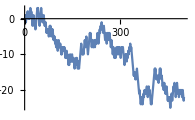

```mathematica
ListLinePlot[NestList[#+RandomChoice[{+1,-1}]&,0,500]]
```

到目前为止，我们已经迭代化地使用 NestList 来高效执行某个特定函数的连续应用。但是你也可以把它用于递归，在递归中，函数的应用模式本身就是嵌套的。

这将连续应用函数 f：

```mathematica
NestList[f[#]&,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

f 的应用模式在这里更为复杂：

```mathematica
NestList[f[#,#]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

添加边框可以更容易地看到究竟发生了什么：

```mathematica
NestList[Framed[f[#,#]]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

把所有东西都放在列中，将显示出函数应用的嵌套模式。

嵌套的边框在每一层都是以两两组合的方式递归：

```mathematica
NestList[Framed[Column[{#,#}]]&,x,3]
```

{x,x
x,x
x
x
x,x
x
x
x
x
x
x
x}

这将给出一系列递归嵌套的网格：

```mathematica
NestList[Framed[Grid[{{#,#},{#,#}}]]&,x,3]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

这就形成了分形结构的起始：

```mathematica
NestList[Framed[Grid[{{0,#},{#,#}}]]&,x,3]
```

{x,0 | x
x | x,0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x,0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x}

很容易就可以得到一些相当华丽的递归结构：

```mathematica
NestList[Flatten[{#,Rotate[#,90°],Rotate[#,270°]}]&,"R",4]
```

{R,{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}}}}

并非所有递归的结果都是如此复杂。这里有一个例子，将一个列表的两个移位副本连续加在一起，比如 {0,1,2,1}+{1,2,1,0}。

在一个列表的前部和后部添加 0，然后加在一起：

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},5]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1}}

如果你把结果放在一个网格中，它就形成了一个二项式系数的帕斯卡三角形：

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1

这里是另一个用 NestList 进行递归的例子。

使用两个函数 f 和 g 组成递归结构：

```mathematica
NestList[{f[#],g[#]}&,x,3]
```

{x,{f[x],g[x]},{f[{f[x],g[x]}],g[{f[x],g[x]}]},{f[{f[{f[x],g[x]}],g[{f[x],g[x]}]}],g[{f[{f[x],g[x]}],g[{f[x],g[x]}]}]}}

即使将它们放置在列中，仍然相当难以理解已经创建的结构。

将递归结构排列成列：

```mathematica
NestList[Column[{f[#],g[#]}]&,x,3]
```

{x,f[x]
g[x],f[f[x]
g[x]]
g[f[x]
g[x]],f[f[f[x]
g[x]]
g[f[x]
g[x]]]
g[f[f[x]
g[x]]
g[f[x]
g[x]]]}

NestGraph 基本上和 NestList 一样，只是它创建的是一个图而不是一个列表。它重复应用一个函数来确定一个特定的节点应该连接到什么节点。在这种情况下，它将产生一个节点树，能够更清楚地了解发生了什么。

从 x 开始，然后反复连接到应用该函数得到的节点列表：

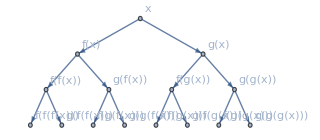

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->All]
```

反复应用一个数字函数，将形成另一个树状结构：

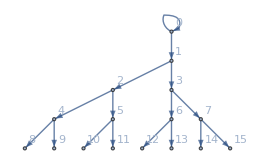

```mathematica
NestGraph[{2#,2#+1}&,0,4,VertexLabels->All]
```

你可以使用 NestGraph 有效地向外“爬行”来创建一个网络。举例来说，我们可以重复应用一个函数，对任何国家都给出与之接壤的国家列表。其结果是一个连接接壤国家的网络，这里从瑞士开始。

从瑞士开始向外“爬行”2步，就能将每个国家与所有与之接壤的国家连接起来：

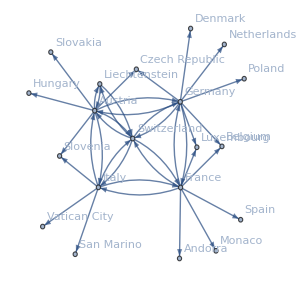

```mathematica
NestGraph[#["BorderingCountries"]&,LinguisticAssistant,2,VertexLabels->All]
```

举另一个例子，从“hello”这个词开始，依次将每个词与 Nearest 认为与它最接近的常见词列表中的 3 个词连接起来。

考虑 1 个字母的变化，建立一个相近单词的网络：

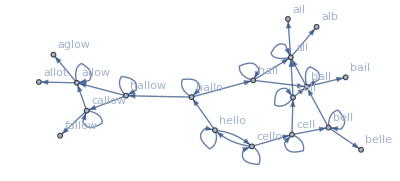

```mathematica
NestGraph[Nearest[WordList[ ],#,3]&,"hello",4,VertexLabels->All]
```

词汇

NestList[f,x,n] |   | 将 f 应用于 x 最多 n 次
Nest[f,x,n] |   | 给出将 f 应用于 x n 次后的结果
NestGraph[f,x,n] |   | 创建从 x 开始嵌套应用 f 的图

"共有 11 道习题"
"以及 5 道附加题" | "开始练习 »"

从光栅化的大小为 30 的 “X” 开始，将 Blur 嵌套最多 10 次的结果创建为一个列表。»

| 期望输出： |  
  | {,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

从 x 开始，然后通过嵌套应用 Framed 最多10次，每次使用随机的背景颜色，形成一个列表。»

| 期望输出示例： |  
  | {x,x,x,x,x,x,x,x,x,x,x} |

从一个大小为 50 的 “A” 开始，然后创建一个嵌套最多 5 次的列表，每次添加一个边框并随机旋转。»

| 期望输出示例： |  
  | {"A","A","A","A","A","A"} |

创建一个逻辑映射迭代 4 #(1-#)& 迭代 100 次的线条图，从 0.2 开始。»

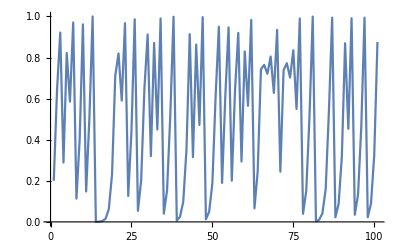
| 期望输出： |  
  | -Graphics- |

计算从 1 开始的 1+1/#& 的 30 次迭代的结果数值。»

| 期望输出： |  
  | 1.61803 |

通过嵌套乘法创建一个 3 的前 10 次方(从 3^0 开始)的列表。»

| 期望输出： |  
  | {1,3,9,27,81,243,729,2187,6561,19683,59049} |

将(牛顿法)函数 (#+2/#)/2&  从 1.0 开始最多嵌套 5 次的结果列出，然后从所有结果中减去 √2。»

| 期望输出： |  
  | {-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16} |

创建一个 1000 步的二维随机行走的图形，它从 {0,0} 开始，在每一步，将在 -1 和 +1 之间的一对随机实数添加到坐标中。»

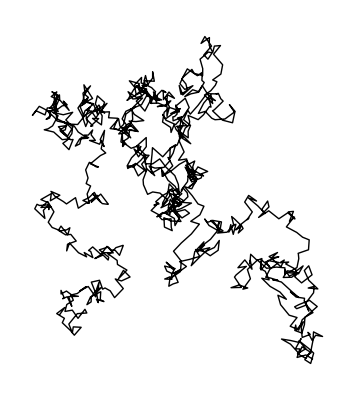
| 期望输出示例： |  
  | -Graphics- |

从 {1} 开始，分别在开头和结尾处连接 {0}，并将连接结果相加后求对 2 的模余的结果，如此嵌套 50 次组成帕斯卡三角形，绘制此三角形的数组图示。»

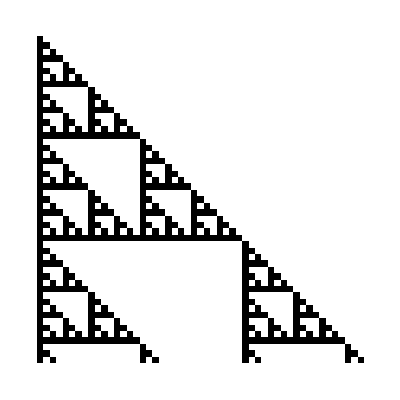
| 期望输出： |  
  | -Graphics- |

生成一个图，从 0 开始，将每个数值为 n 的节点连接到数值为 n+1 和 2n 的节点，如此嵌套 10 次。»

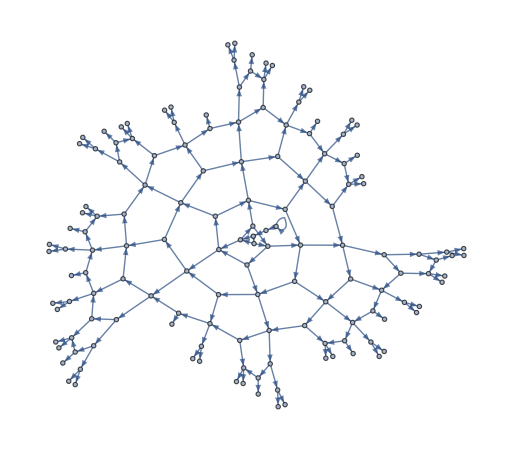
| 期望输出： |  
  | -Graphics- |

生成一个从美国开始嵌套寻找接壤国家的图，进行 4 次迭代。»

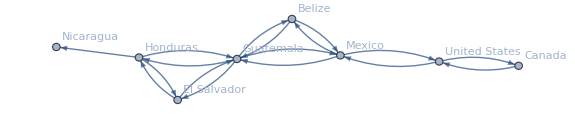
| 期望输出： |  
  | -Graphics- |

创建线性全等函数 Mod[59#,101]& 的 100 次迭代的线条图，从 1 开始。»

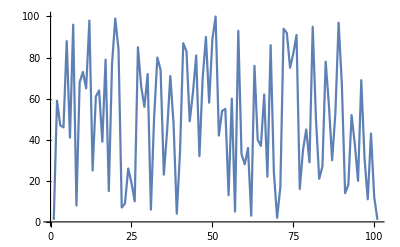
| 期望输出： |  
  | -Graphics- |

创建一个包含 5 个元素的 2 的指数塔的列表，即 2^2^2... n 次方，其中 n 从 0 到 4。»

| 期望输出： |  
  | {1,2,4,16,65536} |

创建一个包含 20 个元素的 1.2 的指数塔的列表，即 1.2^1.2^... n 次方，其中 n 从 0 到 19。»

| 期望输出： |  
  | {1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773} |

生成一个由函数 Sqrt[1+#]& 进行最多 10 次嵌套得到的数值的列表。»

| 期望输出： |  
  | {1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803} |

创建一个 1000 步的三维随机行走的图形，从 {0,0,0} 开始，在每一步，将三个 -1 和 +1 之间的随机实数添加到坐标中。»

| 期望输出： |  
  | -Graphics3D- |

问&答

迭代和递归之间有什么区别？

如果重复地做同一件事，这就是迭代。如果拿着一个操作的结果，在任何地方应用同样的操作，这就是递归。这有点令人困惑，因为递归的简单情况就是迭代。 NestList 总是进行递归，但如果只有一个槽出现在函数中，则递归可以被“展开”为迭代。

嵌套、递归和分形之间有什么关系？

它们的关系非常密切。并没有精确的定义，但分形基本上是表现出某种类型的嵌套或递归结构的几何形式。

什么是帕斯卡三角形？

这是在初级数学中非常常见的一个结构。它的定义与这里的 Wolfram 语言代码非常接近：在每一行，每个数字都被计算为其正上方和其右上方的数字之和。每一行都给出了(1+x)^n 展开的系数。

NestGraph 像一个网络爬虫吗？

在概念上是的。我们可以把它想象成从一个网页开始，然后访问该网页的链接，并继续递归这个过程的类似做法。我们将在第 44 节中看到这样的例子。

为什么有些国家在接壤国家图中没有双向箭头？

如果 NestGraph 运行了足够多的步数，那么所有的国家都会有双向的箭头，因为如果 A 与 B 接壤，那么 B 就与 A 接壤。但在这里，我们只运行了两步就停止了，所以还没有算到许多反向连接。

为什么要用 NestList 来做像 NestList[2*#&,1,15] 这样的事情？

你可以不这样做。你可以直接使用 Power，如 Table[2^n,{n,0,15}]。但能看到连续嵌套产生的 Plus、Times、Power 序列(例如 NestList[2+#&,0,15] 就是 Table[2*n,{n,0,15}])。

有没有一种方法可以一直应用一个函数，直到不再发生任何变化？

有的。使用 FixedPoint 或者 FixedPointList(见第 41 节)。

技术笔记

通过先计算一个 NearestFunction，然后重复使用它，而不是为每个词从头开始计算 Nearest，可以使最接近的词这个例子更有效率。这个例子也与第22节中讨论的 NearestNeighborGraph 密切相关。

探索更多

Wolfram 语言中的函数迭代指南 »